## Normal distribution

### The normal distribution function for a given argument “x” and the set of parameters: xargs -> {standard deviation, mean}

#### xargs=[σ , μ]

```mathematica
ClearAll["Global*`"]
```

```mathematica
fNormal[x_,xargs_]:=1/xargs[[1]]*1/(√(2π))Exp[-1/2*((x-xargs[[2]])/xargs[[1]])^2];
```

```mathematica
data[nsize_,left_,right_]:=Table[x,{x,left,right,(right-left)/nsize}];
mappedData[data_]:=Map[fNormal[#,{0.8,0}]&,data];
normalData[stddev_,mean_,left_,right_]:=Table[{x,fNormal[x,{stddev,mean}]},{x,left,right,(right-left)/50}];
```

```mathematica
plotter[data_,color_]:=ListPlot[Table[{data[[i]],mappedData[data][[i]]},{i,1,Length[data]}],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],Joined->True,PlotMarkers->{Automatic,Tiny},AspectRatio->0.75,FrameLabel->{"x","𝒫(x)"},PlotStyle->{color,Thick},PlotLegends->Placed[{"P(x)"},Scaled[{0.2,0.85}]],ImageSize->Large,LabelStyle->{21,Bold,Black,FontFamily->"Times"}];
```

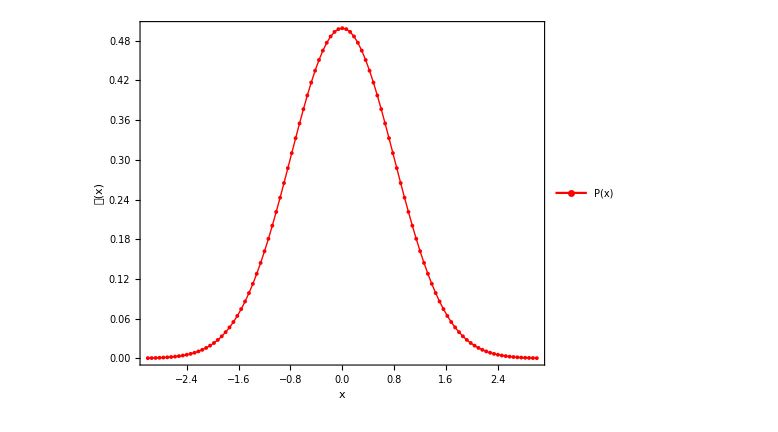

```mathematica
testdata=data[100,-3,3];
Show[plotter[testdata,Red]]
```

## Draw a list plot with marked lines

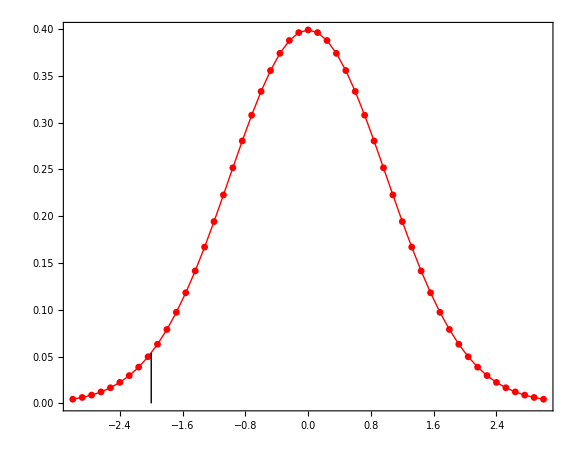

```mathematica
lineplotter[lines_,data_,xargs_]:=ListPlot[data,Frame->True,Joined->True,PlotMarkers->{Automatic, Small},Axes->False,AspectRatio->0.78,ImageSize->Large,FrameStyle->Directive[Black,Thick],PlotStyle->{Red,Thick},Epilog->{Line[{{lines[[1]],0},{lines[[1]],fNormal[lines[[1]],xargs]}}]}];
Show[lineplotter[{-2,1},normalData[1,0,-3,3],{1,0}]]
```